```mathematica
SetDirectory[NotebookDirectory[]]

"/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks"

(*LOAD FUNCTIONS*)

<<MyFunctions`

(*INIITIALIZE PARAMETERS*)
alpha=0.5;
beta=1.0;
delta=0.5;
katta=5;
qAvg=1.0;
eta=0.25;
etaBar=0.5;
chi=0.1;
uBar=1.0;
cp=20.0;
cs=10.0;

(*Number of firms*)
n=10.0;
(*A dummy vector used to identify each firm by a certain number:1-first firm,2-second firm,.....n-nth firm*)
Id=Table[i,{i,1,n}];

(*Number of consumers*)
m=100.0;
```

/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks

/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks

------------------------------------------------------------------------------------------------------------------------------

Exercise 1 c)

------------------------------------------------------------------------------------------------------------------------------

------------------------------------------------------------------------------------------------------------------------------

Results batch runs:

------------------------------------------------------------------------------------------------------------------------------

Number of firms that survive: {10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

The firms which survive: 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

------------------------------------------------------------------------------------------------------------------------------

Plots of last batch run:

------------------------------------------------------------------------------------------------------------------------------

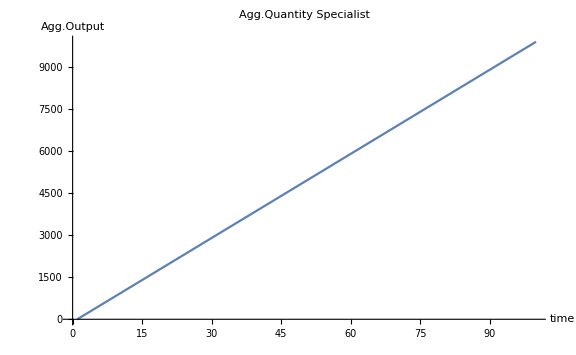

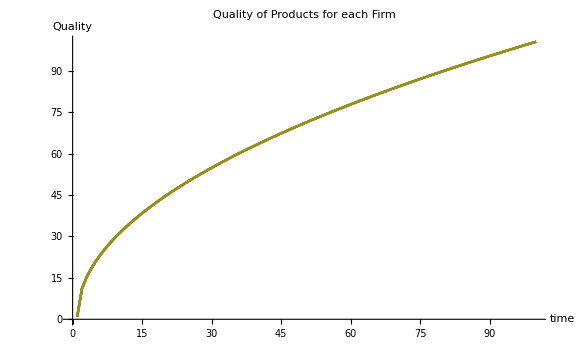

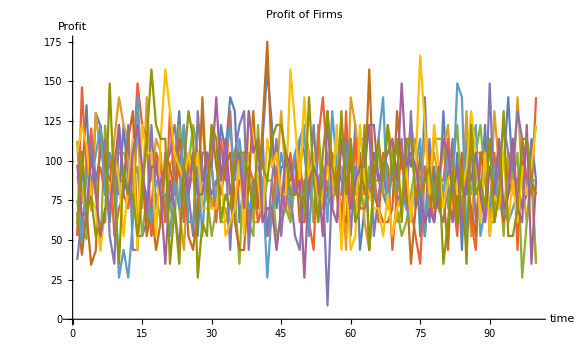

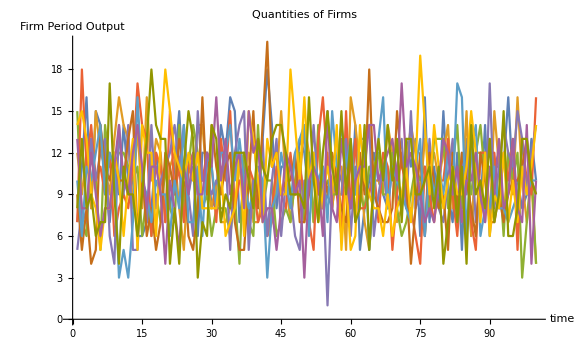

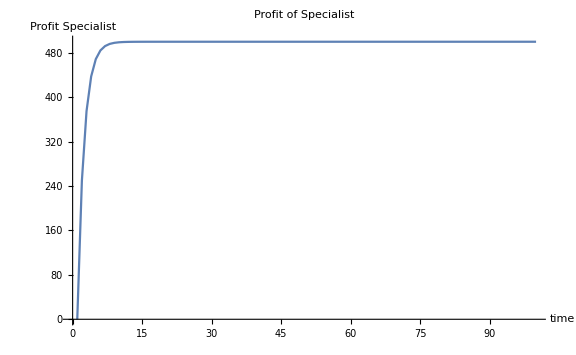

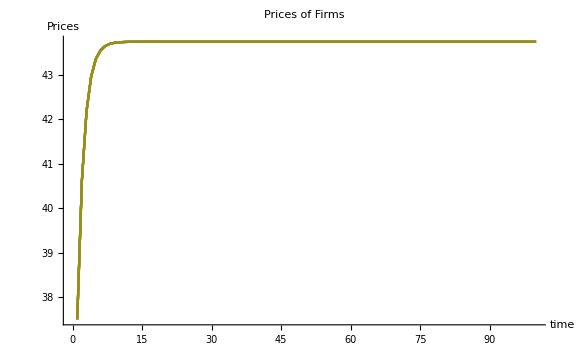

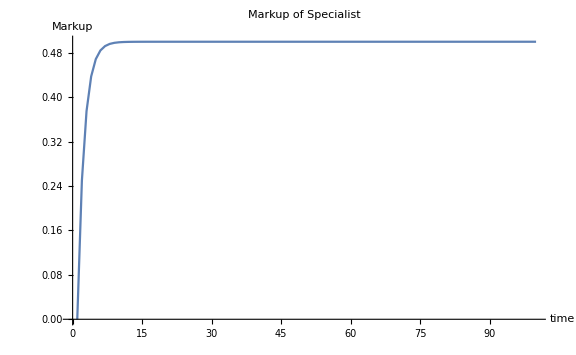

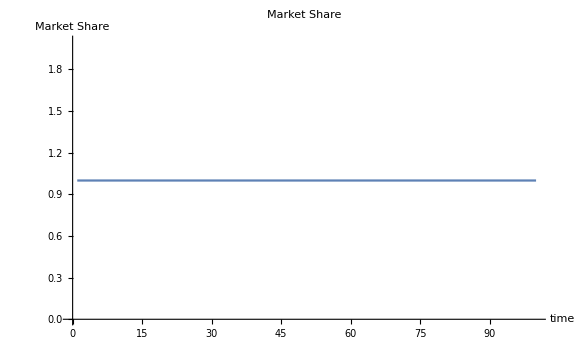

```mathematica
T=100;
R=20;
(*firms making positive profits at T for each batch run*)

survivor=Table[0.0,{r,1,R}];
(*how many firms make positive profits at T?*)

numFirmsSurvive=Table[0.0,{r,1,R}];

Do[(*price of specialist*)
priceSpec=Table[0.0,{i,1,T}];
(*prices of firms*)
priceListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*qualities*)
qualityList=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*quantities produced per Period*)
quantPeriodFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
quantPeriodSpec=Table[0.0,{i,1,T}];
(*aggregated output of firm*)
quantAggFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*aggregated output of specialist*)
quantAggSpec=Table[0.0,{i,1,T}];
(*market share of specialist*)
msSpec=Table[0.0,{i,1,T}];
(*markup of specialist*)
markupSpec=Table[0.0,{i,1,T}];
(*profits of firms*)
profitListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*profit of specialist*)
profitSpec=Table[0.0,{i,1,T}];
(*list of probabilities*)
probList=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*PERIODS*)

Do[(*compute markup*)
If[t==1,markupSpec[[t]]=0.0,markupSpec[[t]]=etaSpec[delta,markupSpec[[t-1]],msSpec[[t-1]],etaBar];];
(*compute price of specialist*)
priceSpec[[t]]=pSpec[cs,markupSpec[[t]]];
(*compute prices of firms*)
priceListFirm[[t]]=Table[pFirmSpec[cSpec[cp,cs,markupSpec[[t]]],eta],{i,1,n}];
(*compute aggregated output of specialist:In the initial period (t=1) the aggregated output is zero!*)
If[t==1,
quantAggSpec[[t]]=0.0,
quantAggSpec[[t]]=quantAggSpec[[t-1]]+quantPeriodSpec[[t-1]]];
(*compute quality using aggregated output of specialist*)
qualityList[[t]]=Table[qualitySpec[uBar,alpha,beta,quantAggSpec[[t]]],{i,1,n}];
(*Compute the probabilities using the quality of the specialits and prices of firms!*)probList[[t]]=Table[probability[i,priceListFirm[[t]],qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll=RandomChoice[probList[[t]]->Id,m];
(*compute quantities produced by firms in period t*)
quantPeriodFirm[[t]]=Table[Count[choiceListAll,i],{i,1,n}];
(*compute quantities produced by specialist in period t*)
quantPeriodSpec[[t]]=Sum[quantPeriodFirm[[t,i]],{i,1,n}];
(*compute market share*)
msSpec[[t]]=ms[t,n,quantPeriodSpec[[t]],quantPeriodFirm];
(*compute profits*)
profitListFirm[[t]]=Table[profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSpec[cp,cs,markupSpec[[t]]]],{i,1,n}];
profitSpec[[t]]=profit[quantPeriodSpec[[t]],priceSpec[[t]],cs];
(*compute statistic*)
If[t==T,numFirmsSurvive[[r]]=Count[profitListFirm[[t]],u_/;u>0];
survivor[[r]]=Position[profitListFirm[[t]],u_/;u>0]],
{t,1,T}],
{r,1,R}];

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Exercise 1 c)"]
Print["------------------------------------------------------------------------------------------------------------------------------"]

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Results batch runs:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Number of firms that survive: ",numFirmsSurvive]
Print["The firms which survive: ",TableForm[Table[Table[survivor[[r,i,1]],{i,1,Length[survivor[[r]]]}],{r,1,R}]]]

(*Print["------------------------------------------------------------------------------------------------------------------------------"] Print["Results of last batch run:"] Print["------------------------------------------------------------------------------------------------------------------------------"] Print["Period Quantities: ",TableForm[quantPeriodFirm]] Print["Prices: ",TableForm[priceListFirm]] Print["Prices: ",TableForm[priceListFirm]] Print["Market Share: ",TableForm[msSpec]] Print["Profit Firms: ",TableForm[profitListFirm]] Print["Profit Specialist: ",TableForm[profitSpec]] Print["Agg. Quantities: ",TableForm[quantAggSpec]] Print["Quality: ",TableForm[qualityList]] Print["Probs: ",TableForm[probList]]*)

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Plots of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
ListPlot[quantAggSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Agg.Quantity Specialist],AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,T}],{j,1,n}],Joined->True,ImageSize->Large,PlotLabel->HoldForm[Quality of Products for each Firm],AxesLabel->{HoldForm[time],HoldForm[Quality]}]
(*plot profit of each firm*)
ListPlot[Table[Table[profitListFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True,PlotRange->All,ImageSize->Large,PlotLabel->HoldForm[Profit of Firms],AxesLabel->{HoldForm[time],HoldForm[Profit]}]
(*plot determinants of profit*)
ListPlot[Table[Table[quantPeriodFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True,ImageSize->Large,PlotLabel->HoldForm[Quantities of Firms],AxesLabel->{HoldForm[time],HoldForm[Firm Period Output]}]
ListPlot[profitSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Profit of Specialist],AxesLabel->{HoldForm[time],HoldForm[Profit Specialist]}]
ListPlot[Table[Table[priceListFirm[[t,j]],{t,1,T}],{j,1,n}],PlotRange->All,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Prices of Firms],AxesLabel->{HoldForm[time],HoldForm[Prices]}]
ListPlot[markupSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Markup of Specialist],AxesLabel->{HoldForm[time],HoldForm[Markup]}]
ListPlot[msSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Market Share],AxesLabel->{HoldForm[time],HoldForm[Market Share]}]
ListPlot[Table[Table[probList[[t,j]],{t,1,T}],{j,1,n}],Joined->True,PlotRange->All,ImageSize->Large,PlotLabel->HoldForm[Evolution of Probabilities for each Firm],AxesLabel->{HoldForm[time],HoldForm[Probs]}]
```